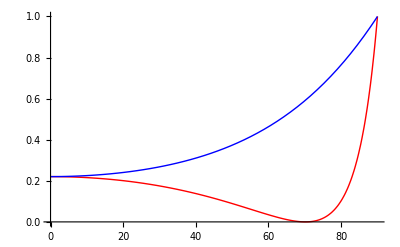

```mathematica
(**********
This program is to calculate reflectivity of a material based on snell's law and Fresnel factor)
**********)

(*Refractive index of incident medium*)
Real1=1;
Imag1=0;
(*Refractive index of incident medium*)
Real2=2.77;
Imag2=0;

(*Calculate Refractive index*)
n1=Abs[Real1+Imag1];
n2=Abs[Real2+Imag2];

(*Fresnel coefficient for p- and s-polarization*)
Rp=Abs[(n1 √(1-(n1/n2 Sin[θ1 °])^2)-n2 Cos[θ1 °])/(n1 √(1-(n1/n2 Sin[θ1 °])^2)+n2 Cos[θ1 °])]^2;
Rs=Abs[(n1 Cos[θ1 °]-n2 √(1-(n1/n2 Sin[θ1 °])^2))/(n1 Cos[θ1 °]+n2 √(1-(n1/n2 Sin[θ1 °])^2))]^2;

(*Plot of Fresnel coefficient 
0 means no reflection (Brewster's angle)*)
Plot[{Rp,Rs},{θ1,0,90},PlotStyle->{Red,Blue}]

;
```